# Mathematica Anashizzle of Atom-output

author: Andreas Weiler (andreas.weiler@cern.ch)

1) should be able to parse all the available information in the JSON (produced from Yaml via the yaml2json tool)
2) should be able to read yoda histogram files (done for HISTO1D)
3) should be user-friendly (done)


TODO

- underflow/overflow example needed
- get more yoda histogramming examples..
- log plot
- scatter2D -> errorbars
- histo2D -> Razor (not supported yet)

Routines for JSON Atom output parsing

```mathematica
<<(NotebookDirectory[]<>"atom_mathematica.m")
```

### Implementation

```mathematica
(*************************)
(*   CROSS SECTION/LUMI/RUN INFO   *)
(*************************)


wdir = NotebookDirectory[];
res=Import[wdir<>"input_files/Qstar_500_truth.json"];
(*ListCuts[res,"ATLAS_1008_2461"]
ShowListCuts[res,"ATLAS_1008_2461"]
*)
(*
ShowCuts[json_,anaName_]:=(Print[Style["FIXME Cutflow for "<>anaName,Bold,Blue]];
header={{"Cut Name","Description","Cut Value","Cut Stat Error"}};
gridP=({#[[1]],#[[2]],#[[4,1,2]]}&/@ListCuts[json,anaName]);
Join[header,gridP]//Grid//Print

(*todo*));

ShowCuts[res,"ATLAS_1008_2461"]*)


(*ShowAtomRunInfo[json_]:= OV[json,"Atom Run Info"];*)
```

### Examples

#### Show Analysis Info

```mathematica
wdir = NotebookDirectory[];
res=Import[wdir<>"input_files/Qstar_500_truth.json"];
```

```mathematica
ShowAnalysisInfo[res,"ATLAS_1008_2461"]
```

ATLAS_1008_2461

Summary : Search for New Particles in Two-Jet Final States in 7 TeV Proton-Proton Collisions with the ATLAS Detector at the LHC

Int. luminosity : 0.00031 1/fb

References : {arXiv:1008.2461}

```mathematica
ShowFullAnalysisInfo[res,"ATLAS_1008_2461"]
```

ATLAS_1008_2461

Summary : Search for New Particles in Two-Jet Final States in 7 TeV Proton-Proton Collisions with the ATLAS Detector at the LHC

Experiment : ATLAS

Year : 2010

Description : A search for new heavy particles manifested as resonances in two-jet final states is presented. The data were produced in 7 TeV proton-proton collisions by the Large Hadron Collider (LHC) and correspond to an integrated luminosity of 315 nb^-1 collected by the ATLAS detector. No resonances were observed. Upper limits were set on the product of cross section and signal acceptance for excited-quark (q*) production as a function of q* mass. These exclude at the 95% CL the q* mass interval 0.30 < mq* < 1.26 TeV, extending the reach of previous experiments.

RunInfo : Search for New Particles in Two-Jet Final States in 7 TeV Proton-Proton Collisions with the ATLAS Detector at the LHC

Status : VALIDATED

Authors : {Christopher Vermilion <verm@uw.edu>, Michele Papucci <papucci@lbl.gov>}

References : {arXiv:1008.2461}

SpiresID : 8755477

InspireID : 865423

BibKey : :2010bc

Int. luminosity : 0.00031 ± 0.035 1/fb

References : {arXiv:1008.2461}

#### Efficiencies

```mathematica
ListEfficiencies[res,"ATLAS_1008_2461"]
```

{{Efficiency,,False,0.133,-0.0015,0.0015},{Efficiency2,,False,0.133,-0.0015,0.0015}}

```mathematica
ListEfficiencies[res,"ATLAS_1008_2461",ShowSubprocesses]
```

{{Efficiency,,False,{{0,0.133,{-0.0015,0.0015}},{147,0.0505,{-0.00097,0.00099}},{148,0.0826,{-0.0012,0.0012}}}},{Efficiency2,,False,{{0,0.133,{-0.0015,0.0015}},{147,0.0505,{-0.00097,0.00099}},{148,0.0826,{-0.0012,0.0012}}}}}

```mathematica
ShowEfficiencies[res,"ATLAS_1008_2461"]
```

Efficiencies for ATLAS_1008_2461

Efficiency Name | Description | IsControlRegion | Efficiency Value | Stat Error - | Stat Error +
Efficiency |  | False | 0.133 | -0.0015 | 0.0015
Efficiency2 |  | False | 0.133 | -0.0015 | 0.0015

```mathematica
GetEfficiency[res,"ATLAS_1008_2461","Efficiency"]
```

{Efficiency,,False,0.133,-0.0015,0.0015}

```mathematica
GetEfficiencyValue[res,"ATLAS_1008_2461","Efficiency"]
```

0.133

```mathematica
GetEfficiencyStatError[res,"ATLAS_1008_2461","Efficiency"]
```

{-0.0015,0.0015}

#### Cuts

```mathematica
ListCuts[res,"ATLAS_1008_2461"]
%//Grid
```

{{J1J2_etaSep,,{J2_etaRange,Passed},{{0,0.155,{None},-0.73,{-0.081,0.081},{None}}}},{J2_etaRange,,{LeadJ_etaRange,Passed},{{0,0.2446,{None},-0.075,{-0.064,0.064},{None}}}},{J2_pT,,{LeadJ_pT,Passed},{{0,0.356,{None},0,{0,0},{None}}}},{LeadJ_etaRange,,{J2_pT,Passed},{{0,0.2948,{None},-0.041,{-0.058,0.058},{None}}}},{LeadJ_pT,,{NumJets,Passed},{{0,0.356,{None},0.541,{-0.053,0.053},{None}}}},{NumJets,,{,Passed},{{0,0.99804,{None},0,{0,0},{None}}}},{mjj,,{J1J2_etaSep,Passed},{{0,0.133,{None},0.18,{-0.087,0.087},{None}}}}}

J1J2_etaSep |  | {J2_etaRange,Passed} | {{0,0.155,{None},-0.73,{-0.081,0.081},{None}}}
J2_etaRange |  | {LeadJ_etaRange,Passed} | {{0,0.2446,{None},-0.075,{-0.064,0.064},{None}}}
J2_pT |  | {LeadJ_pT,Passed} | {{0,0.356,{None},0,{0,0},{None}}}
LeadJ_etaRange |  | {J2_pT,Passed} | {{0,0.2948,{None},-0.041,{-0.058,0.058},{None}}}
LeadJ_pT |  | {NumJets,Passed} | {{0,0.356,{None},0.541,{-0.053,0.053},{None}}}
NumJets |  | {,Passed} | {{0,0.99804,{None},0,{0,0},{None}}}
mjj |  | {J1J2_etaSep,Passed} | {{0,0.133,{None},0.18,{-0.087,0.087},{None}}}

```mathematica
ListCuts[res,"ATLAS_1008_2461",ShowSubprocesses]
```

{{J1J2_etaSep,,{J2_etaRange,Passed},{{0,0.155,{None},-0.73,{-0.081,0.081},{None}},{147,0.059,{None},-0.69,{-0.13,0.13},{None}},{148,0.0957,{None},-0.75,{-0.1,0.1},{None}}}},{J2_etaRange,,{LeadJ_etaRange,Passed},{{0,0.2446,{None},-0.075,{-0.064,0.064},{None}},{147,0.089,{None},-0.12,{-0.11,0.11},{None}},{148,0.156,{None},-0.047,{-0.08,0.081},{None}}}},{J2_pT,,{LeadJ_pT,Passed},{{0,0.356,{None},0,{0,0},{None}},{147,0.126,{None},0,{0,0},{None}},{148,0.2303,{None},0,{0,0},{None}}}},{LeadJ_etaRange,,{J2_pT,Passed},{{0,0.2948,{None},-0.041,{-0.058,0.058},{None}},{147,0.106,{None},-0.05,{-0.097,0.097},{None}},{148,0.189,{None},-0.035,{-0.073,0.073},{None}}}},{LeadJ_pT,,{NumJets,Passed},{{0,0.356,{None},0.541,{-0.053,0.053},{None}},{147,0.126,{None},0.54,{-0.089,0.089},{None}},{148,0.2303,{None},0.54,{-0.066,0.066},{None}}}},{NumJets,,{,Passed},{{0,0.99804,{None},0,{0,0},{None}},{147,0.3483,{None},0,{0,0},{None}},{148,0.6497,{None},0,{0,0},{None}}}},{mjj,,{J1J2_etaSep,Passed},{{0,0.133,{None},0.18,{-0.087,0.087},{None}},{147,0.0505,{None},0.17,{-0.14,0.14},{None}},{148,0.0826,{None},0.19,{-0.11,0.11},{None}}}}}

```mathematica
GetCut[res,"ATLAS_1008_2461","J2_etaRange"]
```

{J2_etaRange,,{LeadJ_etaRange,Passed},{{0,0.2446,{None},-0.075,{-0.064,0.064},{None}}}}

```mathematica
GetCutValue[res,"ATLAS_1008_2461","J2_etaRange"]
```

0.2446

```mathematica
GetCutStatError[res,"ATLAS_1008_2461","J2_etaRange"]
```

{-0.064,0.064}

#### Cross Sections

```mathematica
ListCrossSection[res,ShowSubprocesses]
```

{{0,6425,-29,29},{147,2242,-17,17},{148,4183,-23,23}}

```mathematica
ShowCrossSection[res,ShowSubprocesses]
```

Cross Sections in fb (Process ID = 0 is total xsec)

Process ID | Cross Section | Cross Section Error- | Cross Section Error+
0 | 6425 | -29 | 29
147 | 2242 | -17 | 17
148 | 4183 | -23 | 23

```mathematica
GetTotalCrossSection[res]
```

{6425,-29,29}

Routines for YODA plotting

from: https://yoda.hepforge.org/trac/wiki/DataFormat

### Examples

GetYodaRaw get’s a list of histograms or plots.

```mathematica
test=(GetYodaRaw[wdir<>"input_files/Qstar_500_truth.yoda"]);
```

1 Imported ..Histo1D..  /ATLAS_1008_2461/d01-x01-y01/0

2 Imported ..Histo1D..  /ATLAS_1008_2461/d01-x01-y01/147

3 Imported ..Histo1D..  /ATLAS_1008_2461/d01-x01-y01/148

This contains Hist1D objects:

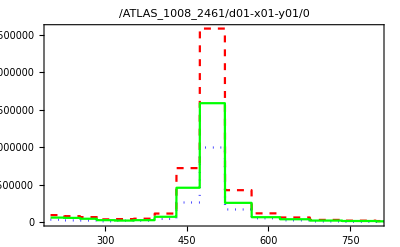

```mathematica
h1=HistogramPlot[test[[1]],PlotStyle->{Dashed,Red}];
h2=HistogramPlot[test[[2]],PlotStyle->{Dotted,Blue}];
h3=HistogramPlot[test[[3]],PlotStyle->Green];
Show[h1,h2,h3,PlotRange->{{200,800},All}]
```

This contains Scatter2D objects:

```mathematica
test=(GetYodaRaw[wdir<>"input_files/scatter2D.yoda"]);
```

1 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d01-x01-y01

2 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d01-x01-y02

3 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d02-x01-y01

4 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d03-x01-y01

5 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d04-x01-y01

6 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d05-x01-y01

7 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d06-x01-y01

8 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d07-x01-y01

9 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d08-x01-y01

10 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d09-x01-y01

11 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d10-x01-y01

12 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d11-x01-y01

13 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d12-x01-y01

14 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d13-x01-y01

15 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d14-x01-y01

16 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d15-x01-y01

17 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d16-x01-y01

18 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d17-x01-y01

19 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d18-x01-y01

20 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d19-x01-y01

21 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d20-x01-y01

22 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d21-x01-y01

23 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d22-x01-y01

24 Imported ..Scatter2D..  /REF/ZEUS_2001_S4815815/d23-x01-y01

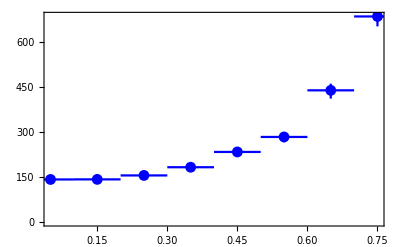

```mathematica
hh=ScatterPlot[test[[2]],PlotStyle->{Blue},PlotRange->All]
```

```mathematica
7./30.
```

0.233333

# attic

```mathematica
(*tempYoda=Split[tempYoda2,StringMatchQ[#,"Path"]&]*)
	tempYoda= SplitBy[tempYoda,delimiterQ[#[[1]]]&];
(*outNew={};
Do[
AppendTo[outNew, {tempYoda[[n]],tempYoda[[n+1]]}],
{n,1,Length[tempYoda]/2}];
out=outNew*)
Print["Contains ", Length[tempYoda]/2," Histograms"];
out={#[[1]],#[[2]]}&/@tempYoda
```

```mathematica
OV:=OptionValue; (*save space*)

(* all the contents of an analysis*)
PickAnalysis[json_,anaName_]:=OV[OV[{json},"Analyses"],anaName];

GetVal[json_,entrName_]:=OV[OV[json,entrName],"Value"];
GetVal[json_,entrName_,valName_]:=OV[OV[json,valName],valName]; (*e.g. for "Cut Value"*)

PrintValue[json_,valName_]:=Print[ Style[valName <> " : " ,Blue], ToString[OV[ana,valName]]]; (* for simple Value/Error pairs *)

(*************************)
(*       PRINT OUTPUT    *)
(*************************)

ShowAnalysisInfo[json_,anaName_]:=
(
ana=PickAnalysis[json,anaName];
Print[ Style[anaName,Bold]];
PrintValue[ana,"Summary"];
Print[ Style["Int. luminosity : ",Blue]  , ToString[GetVal[ana,"Luminosity"]/1000.] <> " 1/fb "];
PrintValue[ana,"References"];
);



ShowFullAnalysisInfo[json_,anaName_]:= 
(
ana=PickAnalysis[json,anaName];
Print[ Style[anaName,Bold,Blue]];
PrintValue[ana,"Summary"];
PrintValue[ana,"Experiment"];
PrintValue[ana,"Year"];
PrintValue[ana,"Description"];
PrintValue[ana,"RunInfo"];
PrintValue[ana,"Status"];
PrintValue[ana,"Authors"];
PrintValue[ana,"References"];
PrintValue[ana,"SpiresID"];
PrintValue[ana,"InspireID"];

PrintValue[ana,"BibKey"];
Print[ Style["Int. luminosity : ",Blue]  , ToString[GetVal[ana,"Luminosity"]/1000.] <> " ± " <>  ToString[OV[OV[ana,"Luminosity"],"Error"]]<>" 1/fb "];
PrintValue[ana,"References"];

);
(*************************)
(*   EXTRACT EFFIENCIES   *)
(*************************)

ListEfficiencies[json_,anaName_,ShowSubprocesses]:=(
ana=PickAnalysis[json,anaName];
{OV[#,"Efficiency Name"],OV[#,"Description"],OV[#,"IsControlRegion"], ({OV[#,"Sub-process ID"],OV[#,"Efficiency Value"],OV[#,"Efficiency Stat Error"]}&/@OV[#,"Data"])}&  /@ OV[ana,"Efficiencies"]

(*{OV[#,"Name"],OV[#,"Value"],OV[OV[#,"Error"],"Stat"] ,OV[#,"Sub-process ID"] }& /@{OV[#,"Efficiency Name"],OV[#,"Description"],OV[OV[#,"Error"],"Stat"] ,OV[#,"Sub-process ID"] }& *)
);

ShowListEfficiencies[json_,anaName_]:=(
Print[Style["Efficiencies for "<>anaName,Blue,Bold]];
Join[{{"Efficiency Name","Description","IsControlRegion","Efficiency Value","Stat Error -","Stat Error +"}}, ListEfficiencies[json,anaName]]//Grid
);

GetTotEfficiency[jsonEffiency_]:= (Select[({OV[#,"Sub-process ID"],OV[#,"Efficiency Value"],OV[#,"Efficiency Stat Error"]}&/@OV[jsonEffiency,"Data"]),#[[1]]==0&][[1,2]]);

GetTotStatError[jsonEffiency_]:= (Select[({OV[#,"Sub-process ID"],OV[#,"Efficiency Value"],OV[#,"Efficiency Stat Error"]}&/@OV[jsonEffiency,"Data"]),#[[1]]==0&][[1,3]]);

ListEfficiencies[json_,anaName_]:=(
ana=PickAnalysis[json,anaName];
temp={OV[#,"Efficiency Name"],OV[#,"Description"],OV[#,"IsControlRegion"], GetTotEfficiency[#], GetTotStatError[#][[1]],GetTotStatError[#][[2]]}&  /@ OV[ana,"Efficiencies"]

(*{OV[#,"Name"],OV[#,"Value"],OV[OV[#,"Error"],"Stat"] ,OV[#,"Sub-process ID"] }& /@{OV[#,"Efficiency Name"],OV[#,"Description"],OV[OV[#,"Error"],"Stat"] ,OV[#,"Sub-process ID"] }& *)
);

GetEfficiency[json_,anaName_,effName_]:= (
ana=PickAnalysis[json,anaName];
Select[{OV[#,"Efficiency Name"],OV[#,"Description"],OV[#,"IsControlRegion"], GetTotEfficiency[#], GetTotStatError[#][[1]],GetTotStatError[#][[2]]}&  /@ OV[ana,"Efficiencies"],#[[1]]==effName&][[1]]
);

GetEfficiencyValue[json_,anaName_,effName_]:= (
GetEfficiency[json,anaName,effName][[4]]
);

GetEfficiencyStatError[json_,anaName_,effName_]:= (
GetEfficiency[json,anaName,effName][[5;;6]]
);

(*************************)
(*   EXTRACT CUTS   *)
(*************************)


GetSubProc0[jsonSub_]:=Select[jsonSub,#[[1]]==0&][[1]];(* assumes that procID is first entry! *)

ListCuts[json_,anaName_,ShowSubprocesses]:=(
ana=PickAnalysis[json,anaName];
temp={
OV[#,"Cut Name"],
OV[#,"Description"],
OV[#,"Parent Cut"], 
({OV[#,"Sub-process ID"],
OV[#,"Cut Value"],
OV[#,"Cut Value Flags"],
OV[#,"Cut Log. Derivative"],
OV[#,"Cut Log. Der. Stat Error"],
OV[#,"Cut Log. Der. Flags"]
}&
/@OV[#,"Data"])}&  
/@ OV[ana,"Cuts"]

);

ListCuts[json_,anaName_]:=(
{#[[1]],#[[2]],#[[3]],Select[#[[4]],#[[1]]==0&]}&/@ ListCuts[json,anaName,ShowSubprocesses]
);


ShowListCuts[json_,anaName_]:=(
Print[Style[ " Cutflow for " <> anaName,Bold,Blue]]
(* todo *)
);


GetCut[json_,anaName_,cutName_,ShowSubprocesses]:= (
Select[ListCuts[json,anaName,ShowSubprocesses],#[[1]]==cutName&][[1]]
);

GetCut[json_,anaName_,cutName_]:= (
Select[ListCuts[json,anaName],#[[1]]==cutName&][[1]]
);

GetCutValue[json_,anaName_,effName_]:= (
GetCut[json,anaName,effName][[4,1,2]]
);

GetCutStatError[json_,anaName_,effName_]:= (
GetCut[json,anaName,effName][[4,1,5;;6]][[1]]
);
```

```mathematica
GetHistRaw[fileName_]:= 
(
tempYoda=Import[fileName,"Table"];
posL=Position[tempYoda,{"#","BEGIN",___}]//Flatten;

nHistos = Length[ posL ];
outHistos={};

(*
Collect histograms into list,
with position of beginning of histos 'posL', 
split output into lists,
be careful with last histo which goes from 'BEGIN' to the end of the file
*)

Do[
AppendTo[outHistos,
 (*cleanup comments*)
DeleteCases[ 
tempYoda⟦ posL[[i]] ;; If[ i < nHistos  , posL[[i+1]]-1, Length[tempYoda] ] ⟧ 
,{"#",___}|{"###",___}|{}
]
];
,{i,nHistos}
];

outHistos

);

HistogramPlot[histo_,HistogramOptions___]:=Module[{high,low,plotInput,HistData,HistTitle,overFlow,underFlow,Nbins,HistTitleString},

HistTitle=Select[histo,StringMatchQ[#[[1]],"Path="~~___]&];
HistTitleString=StringSplit[HistTitle[[1,1]],"="][[2]];

underFlow = Select[histo,StringMatchQ[#[[1]],"Underflow"~~___]&]; (* TODO: Implement, need example*)
overFlow=Select[histo,StringMatchQ[#[[1]],"Overflow"~~___]&]; (* TODO: Implement, need example*)

HistData=Select[histo,NumericQ[#[[1]]]&];

plotInput = {#[[3]],#[[1]] ≤x<#[[2]]}& /@ HistData;

low = First[HistData][[1]];
high=Last[HistData][[1]];
Nbins=Length[HistData];

Plot[Piecewise[plotInput],{x,low,high},HistogramOptions,PlotRange->All,Exclusions->None,PlotPoints->3(Nbins),Frame->True,PlotLabel->HistTitleString]
];
```